```mathematica
t = {12,20,30};
q = {5,3,2}; ordGroup=60;nmax=500;

(*An alternative way to compute S(n)*)
(*For[n=1,n≤nmax,n++,
ss[n]=IntegerPart[n/q[[1]]]+IntegerPart[n/q[[2]]]+IntegerPart[n/q[[3]]]-n+1];*)
```

```mathematica
(*Set to True to calculate # of equations based only on even subspaces*)
fullGroup = False;
If[fullGroup,fg=2,fg=1];
```

```mathematica
rt[0]=0;
For[n=0,n≤nmax,n++,
(*Find set Q* *)
Q = { };
Do[If[Mod[n,q[[j]]]≠0,Q=Append[Q,t[[j]]]],{j,1,3}]
(*Use Sobolev formula for S(n)*)
If[(2n+1)≤Total[Q],s[n] = IntegerPart[(2n+1)/ordGroup],s[n] = IntegerPart[(2n+1)/ordGroup]+1];
(*Keep running total of number of equations*)
If[fullGroup,rt[n+1]=If[EvenQ[n],rt[n]+s[n],rt[n]],
rt[n+1]=rt[n]+s[n]]
];
```

```mathematica
(*Type of quadrature to use*)
(*itype = 1 -> vertices and general points*)
(*itype = 2 -> vertices, face-centers and general points*)
(*itype = 3 -> vertices, edge-midpoints and general points*)
(*itype = 4 -> vertices, face-centers, edge-midpoints and general points*)
(*itype = 5 -> vertices, two points fixed on each edge and general points*)
itype=1;mp=1;
If[itype==1, fc=0;ec=0,If[itype==2,fc=1;ec=0,If[itype==3,fc=0;ec=1,If[itype==4,fc=1;ec=1,If[itype==5,fc=0;ec=1;mp=2]]]]];
For[n=0,n≤nmax,n++,
ngens[n]=(rt[n+1]-1-fc-ec)/3 ;                 (*Number of generators*)
rgens[n] =Ceiling[ngens[n]];                              (*Number of generators rounded up*)
unknowns[n]=1+fc+ec+3rgens[n];                  (*Number of unknows*)
excess[n]=unknowns[n]-rt[n+1];                     (*unknowns - # of eqs*)
nnodes[n]=12+20fc+ mp 30ec+fg 60rgens[n];  (*Number of nodes*)
eff[n] = (n+1)^2/(3nnodes[n])//N                (*Efficiency*)
]
```

```mathematica
TableForm[Table[{n,s[n],rt[n+1],ngens[n],rgens[n],unknowns[n],excess[n],eff[n],nnodes[n]},{n,0,nmax}],TableHeadings->{None,{"n","S(n)","Total # eqs","# Generators","# Gen rounded","# unknowns","Excess variables","Eff.","# of nodes"}}]
```

n | S(n) | Total # eqs | # Generators | # Gen rounded | # unknowns | Excess variables | Eff. | # of nodes
0 | 1 | 1 | 0 | 0 | 1 | 0 | 0.0277778 | 12
1 | 0 | 1 | 0 | 0 | 1 | 0 | 0.111111 | 12
2 | 0 | 1 | 0 | 0 | 1 | 0 | 0.25 | 12
3 | 0 | 1 | 0 | 0 | 1 | 0 | 0.444444 | 12
4 | 0 | 1 | 0 | 0 | 1 | 0 | 0.694444 | 12
5 | 0 | 1 | 0 | 0 | 1 | 0 | 1. | 12
6 | 1 | 2 | 1/3 | 1 | 4 | 2 | 0.226852 | 72
7 | 0 | 2 | 1/3 | 1 | 4 | 2 | 0.296296 | 72
8 | 0 | 2 | 1/3 | 1 | 4 | 2 | 0.375 | 72
9 | 0 | 2 | 1/3 | 1 | 4 | 2 | 0.462963 | 72
10 | 1 | 3 | 2/3 | 1 | 4 | 1 | 0.560185 | 72
11 | 0 | 3 | 2/3 | 1 | 4 | 1 | 0.666667 | 72
12 | 1 | 4 | 1 | 1 | 4 | 0 | 0.782407 | 72
13 | 0 | 4 | 1 | 1 | 4 | 0 | 0.907407 | 72
14 | 0 | 4 | 1 | 1 | 4 | 0 | 1.04167 | 72
15 | 1 | 5 | 4/3 | 2 | 7 | 2 | 0.646465 | 132
16 | 1 | 6 | 5/3 | 2 | 7 | 1 | 0.729798 | 132
17 | 0 | 6 | 5/3 | 2 | 7 | 1 | 0.818182 | 132
18 | 1 | 7 | 2 | 2 | 7 | 0 | 0.911616 | 132
19 | 0 | 7 | 2 | 2 | 7 | 0 | 1.0101 | 132
20 | 1 | 8 | 7/3 | 3 | 10 | 2 | 0.765625 | 192
21 | 1 | 9 | 8/3 | 3 | 10 | 1 | 0.840278 | 192
22 | 1 | 10 | 3 | 3 | 10 | 0 | 0.918403 | 192
23 | 0 | 10 | 3 | 3 | 10 | 0 | 1. | 192
24 | 1 | 11 | 10/3 | 4 | 13 | 2 | 0.82672 | 252
25 | 1 | 12 | 11/3 | 4 | 13 | 1 | 0.89418 | 252
26 | 1 | 13 | 4 | 4 | 13 | 0 | 0.964286 | 252
27 | 1 | 14 | 13/3 | 5 | 16 | 2 | 0.837607 | 312
28 | 1 | 15 | 14/3 | 5 | 16 | 1 | 0.898504 | 312
29 | 0 | 15 | 14/3 | 5 | 16 | 1 | 0.961538 | 312
30 | 2 | 17 | 16/3 | 6 | 19 | 2 | 0.861111 | 372
31 | 2 | 19 | 6 | 6 | 19 | 0 | 0.917563 | 372
32 | 2 | 21 | 20/3 | 7 | 22 | 1 | 0.840278 | 432
33 | 2 | 23 | 22/3 | 8 | 25 | 2 | 0.783198 | 492
34 | 2 | 25 | 8 | 8 | 25 | 0 | 0.829946 | 492
35 | 2 | 27 | 26/3 | 9 | 28 | 1 | 0.782609 | 552
36 | 2 | 29 | 28/3 | 10 | 31 | 2 | 0.745643 | 612
37 | 2 | 31 | 10 | 10 | 31 | 0 | 0.786492 | 612
38 | 2 | 33 | 32/3 | 11 | 34 | 1 | 0.754464 | 672
39 | 2 | 35 | 34/3 | 12 | 37 | 2 | 0.728597 | 732
40 | 2 | 37 | 12 | 12 | 37 | 0 | 0.765483 | 732
41 | 2 | 39 | 38/3 | 13 | 40 | 1 | 0.742424 | 792
42 | 2 | 41 | 40/3 | 14 | 43 | 2 | 0.723396 | 852
43 | 2 | 43 | 14 | 14 | 43 | 0 | 0.757433 | 852
44 | 2 | 45 | 44/3 | 15 | 46 | 1 | 0.740132 | 912
45 | 2 | 47 | 46/3 | 16 | 49 | 2 | 0.725652 | 972
46 | 2 | 49 | 16 | 16 | 49 | 0 | 0.757545 | 972
47 | 2 | 51 | 50/3 | 17 | 52 | 1 | 0.744186 | 1032
48 | 2 | 53 | 52/3 | 18 | 55 | 2 | 0.732906 | 1092
49 | 2 | 55 | 18 | 18 | 55 | 0 | 0.763126 | 1092
50 | 2 | 57 | 56/3 | 19 | 58 | 1 | 0.752604 | 1152
51 | 2 | 59 | 58/3 | 20 | 61 | 2 | 0.743674 | 1212
52 | 2 | 61 | 20 | 20 | 61 | 0 | 0.772552 | 1212
53 | 2 | 63 | 62/3 | 21 | 64 | 1 | 0.764151 | 1272
54 | 2 | 65 | 64/3 | 22 | 67 | 2 | 0.757007 | 1332
55 | 2 | 67 | 22 | 22 | 67 | 0 | 0.784785 | 1332
56 | 2 | 69 | 68/3 | 23 | 70 | 1 | 0.778017 | 1392
57 | 2 | 71 | 70/3 | 24 | 73 | 2 | 0.772268 | 1452
58 | 2 | 73 | 24 | 24 | 73 | 0 | 0.799128 | 1452
59 | 2 | 75 | 74/3 | 25 | 76 | 1 | 0.793651 | 1512
60 | 3 | 78 | 77/3 | 26 | 79 | 1 | 0.789016 | 1572
61 | 3 | 81 | 80/3 | 27 | 82 | 1 | 0.785131 | 1632
62 | 3 | 84 | 83/3 | 28 | 85 | 1 | 0.781915 | 1692
63 | 3 | 87 | 86/3 | 29 | 88 | 1 | 0.7793 | 1752
64 | 3 | 90 | 89/3 | 30 | 91 | 1 | 0.777226 | 1812
65 | 3 | 93 | 92/3 | 31 | 94 | 1 | 0.775641 | 1872
66 | 3 | 96 | 95/3 | 32 | 97 | 1 | 0.7745 | 1932
67 | 3 | 99 | 98/3 | 33 | 100 | 1 | 0.773762 | 1992
68 | 3 | 102 | 101/3 | 34 | 103 | 1 | 0.773392 | 2052
69 | 3 | 105 | 104/3 | 35 | 106 | 1 | 0.773359 | 2112
70 | 3 | 108 | 107/3 | 36 | 109 | 1 | 0.773634 | 2172
71 | 3 | 111 | 110/3 | 37 | 112 | 1 | 0.774194 | 2232
72 | 3 | 114 | 113/3 | 38 | 115 | 1 | 0.775015 | 2292
73 | 3 | 117 | 116/3 | 39 | 118 | 1 | 0.776077 | 2352
74 | 3 | 120 | 119/3 | 40 | 121 | 1 | 0.777363 | 2412
75 | 3 | 123 | 122/3 | 41 | 124 | 1 | 0.778857 | 2472
76 | 3 | 126 | 125/3 | 42 | 127 | 1 | 0.780542 | 2532
77 | 3 | 129 | 128/3 | 43 | 130 | 1 | 0.782407 | 2592
78 | 3 | 132 | 131/3 | 44 | 133 | 1 | 0.784439 | 2652
79 | 3 | 135 | 134/3 | 45 | 136 | 1 | 0.786627 | 2712
80 | 3 | 138 | 137/3 | 46 | 139 | 1 | 0.788961 | 2772
81 | 3 | 141 | 140/3 | 47 | 142 | 1 | 0.791431 | 2832
82 | 3 | 144 | 143/3 | 48 | 145 | 1 | 0.79403 | 2892
83 | 3 | 147 | 146/3 | 49 | 148 | 1 | 0.796748 | 2952
84 | 3 | 150 | 149/3 | 50 | 151 | 1 | 0.799579 | 3012
85 | 3 | 153 | 152/3 | 51 | 154 | 1 | 0.802517 | 3072
86 | 3 | 156 | 155/3 | 52 | 157 | 1 | 0.805556 | 3132
87 | 3 | 159 | 158/3 | 53 | 160 | 1 | 0.808688 | 3192
88 | 3 | 162 | 161/3 | 54 | 163 | 1 | 0.811911 | 3252
89 | 3 | 165 | 164/3 | 55 | 166 | 1 | 0.815217 | 3312
90 | 4 | 169 | 56 | 56 | 169 | 0 | 0.818604 | 3372
91 | 4 | 173 | 172/3 | 58 | 175 | 2 | 0.807942 | 3492
92 | 4 | 177 | 176/3 | 59 | 178 | 1 | 0.811655 | 3552
93 | 4 | 181 | 60 | 60 | 181 | 0 | 0.81543 | 3612
94 | 4 | 185 | 184/3 | 62 | 187 | 2 | 0.806091 | 3732
95 | 4 | 189 | 188/3 | 63 | 190 | 1 | 0.810127 | 3792
96 | 4 | 193 | 64 | 64 | 193 | 0 | 0.814209 | 3852
97 | 4 | 197 | 196/3 | 66 | 199 | 2 | 0.805975 | 3972
98 | 4 | 201 | 200/3 | 67 | 202 | 1 | 0.810268 | 4032
99 | 4 | 205 | 68 | 68 | 205 | 0 | 0.814598 | 4092
100 | 4 | 209 | 208/3 | 70 | 211 | 2 | 0.807297 | 4212
101 | 4 | 213 | 212/3 | 71 | 214 | 1 | 0.811798 | 4272
102 | 4 | 217 | 72 | 72 | 217 | 0 | 0.816328 | 4332
103 | 4 | 221 | 220/3 | 74 | 223 | 2 | 0.809823 | 4452
104 | 4 | 225 | 224/3 | 75 | 226 | 1 | 0.814495 | 4512
105 | 4 | 229 | 76 | 76 | 229 | 0 | 0.819189 | 4572
106 | 4 | 233 | 232/3 | 78 | 235 | 2 | 0.81337 | 4692
107 | 4 | 237 | 236/3 | 79 | 238 | 1 | 0.818182 | 4752
108 | 4 | 241 | 80 | 80 | 241 | 0 | 0.823012 | 4812
109 | 4 | 245 | 244/3 | 82 | 247 | 2 | 0.817789 | 4932
110 | 4 | 249 | 248/3 | 83 | 250 | 1 | 0.822716 | 4992
111 | 4 | 253 | 84 | 84 | 253 | 0 | 0.827659 | 5052
112 | 4 | 257 | 256/3 | 86 | 259 | 2 | 0.822957 | 5172
113 | 4 | 261 | 260/3 | 87 | 262 | 1 | 0.827982 | 5232
114 | 4 | 265 | 88 | 88 | 265 | 0 | 0.833018 | 5292
115 | 4 | 269 | 268/3 | 90 | 271 | 2 | 0.828776 | 5412
116 | 4 | 273 | 272/3 | 91 | 274 | 1 | 0.833882 | 5472
117 | 4 | 277 | 92 | 92 | 277 | 0 | 0.838997 | 5532
118 | 4 | 281 | 280/3 | 94 | 283 | 2 | 0.835162 | 5652
119 | 4 | 285 | 284/3 | 95 | 286 | 1 | 0.840336 | 5712
120 | 5 | 290 | 289/3 | 97 | 292 | 2 | 0.83682 | 5832
121 | 5 | 295 | 98 | 98 | 295 | 0 | 0.842046 | 5892
122 | 5 | 300 | 299/3 | 100 | 301 | 1 | 0.838822 | 6012
123 | 5 | 305 | 304/3 | 102 | 307 | 2 | 0.835834 | 6132
124 | 5 | 310 | 103 | 103 | 310 | 0 | 0.841139 | 6192
125 | 5 | 315 | 314/3 | 105 | 316 | 1 | 0.838403 | 6312
126 | 5 | 320 | 319/3 | 107 | 322 | 2 | 0.835873 | 6432
127 | 5 | 325 | 108 | 108 | 325 | 0 | 0.841241 | 6492
128 | 5 | 330 | 329/3 | 110 | 331 | 1 | 0.838929 | 6612
129 | 5 | 335 | 334/3 | 112 | 337 | 2 | 0.836799 | 6732
130 | 5 | 340 | 113 | 113 | 340 | 0 | 0.842216 | 6792
131 | 5 | 345 | 344/3 | 115 | 346 | 1 | 0.840278 | 6912
132 | 5 | 350 | 349/3 | 117 | 352 | 2 | 0.8385 | 7032
133 | 5 | 355 | 118 | 118 | 355 | 0 | 0.843956 | 7092
134 | 5 | 360 | 359/3 | 120 | 361 | 1 | 0.842346 | 7212
135 | 5 | 365 | 364/3 | 122 | 367 | 2 | 0.84088 | 7332
136 | 5 | 370 | 123 | 123 | 370 | 0 | 0.846365 | 7392
137 | 5 | 375 | 374/3 | 125 | 376 | 1 | 0.845048 | 7512
138 | 5 | 380 | 379/3 | 127 | 382 | 2 | 0.843859 | 7632
139 | 5 | 385 | 128 | 128 | 385 | 0 | 0.849367 | 7692
140 | 5 | 390 | 389/3 | 130 | 391 | 1 | 0.84831 | 7812
141 | 5 | 395 | 394/3 | 132 | 397 | 2 | 0.847369 | 7932
142 | 5 | 400 | 133 | 133 | 400 | 0 | 0.852895 | 7992
143 | 5 | 405 | 404/3 | 135 | 406 | 1 | 0.852071 | 8112
144 | 5 | 410 | 409/3 | 137 | 412 | 2 | 0.851352 | 8232
145 | 5 | 415 | 138 | 138 | 415 | 0 | 0.85689 | 8292
146 | 5 | 420 | 419/3 | 140 | 421 | 1 | 0.856277 | 8412
147 | 5 | 425 | 424/3 | 142 | 427 | 2 | 0.855759 | 8532
148 | 5 | 430 | 143 | 143 | 430 | 0 | 0.861305 | 8592
149 | 5 | 435 | 434/3 | 145 | 436 | 1 | 0.860882 | 8712
150 | 6 | 441 | 440/3 | 147 | 442 | 1 | 0.860545 | 8832
151 | 6 | 447 | 446/3 | 149 | 448 | 1 | 0.860292 | 8952
152 | 6 | 453 | 452/3 | 151 | 454 | 1 | 0.860119 | 9072
153 | 6 | 459 | 458/3 | 153 | 460 | 1 | 0.860023 | 9192
154 | 6 | 465 | 464/3 | 155 | 466 | 1 | 0.860001 | 9312
155 | 6 | 471 | 470/3 | 157 | 472 | 1 | 0.860051 | 9432
156 | 6 | 477 | 476/3 | 159 | 478 | 1 | 0.860169 | 9552
157 | 6 | 483 | 482/3 | 161 | 484 | 1 | 0.860353 | 9672
158 | 6 | 489 | 488/3 | 163 | 490 | 1 | 0.8606 | 9792
159 | 6 | 495 | 494/3 | 165 | 496 | 1 | 0.860909 | 9912
160 | 6 | 501 | 500/3 | 167 | 502 | 1 | 0.861277 | 10032
161 | 6 | 507 | 506/3 | 169 | 508 | 1 | 0.861702 | 10152
162 | 6 | 513 | 512/3 | 171 | 514 | 1 | 0.862182 | 10272
163 | 6 | 519 | 518/3 | 173 | 520 | 1 | 0.862715 | 10392
164 | 6 | 525 | 524/3 | 175 | 526 | 1 | 0.863299 | 10512
165 | 6 | 531 | 530/3 | 177 | 532 | 1 | 0.863933 | 10632
166 | 6 | 537 | 536/3 | 179 | 538 | 1 | 0.864614 | 10752
167 | 6 | 543 | 542/3 | 181 | 544 | 1 | 0.865342 | 10872
168 | 6 | 549 | 548/3 | 183 | 550 | 1 | 0.866115 | 10992
169 | 6 | 555 | 554/3 | 185 | 556 | 1 | 0.866931 | 11112
170 | 6 | 561 | 560/3 | 187 | 562 | 1 | 0.867788 | 11232
171 | 6 | 567 | 566/3 | 189 | 568 | 1 | 0.868687 | 11352
172 | 6 | 573 | 572/3 | 191 | 574 | 1 | 0.869625 | 11472
173 | 6 | 579 | 578/3 | 193 | 580 | 1 | 0.8706 | 11592
174 | 6 | 585 | 584/3 | 195 | 586 | 1 | 0.871613 | 11712
175 | 6 | 591 | 590/3 | 197 | 592 | 1 | 0.872662 | 11832
176 | 6 | 597 | 596/3 | 199 | 598 | 1 | 0.873745 | 11952
177 | 6 | 603 | 602/3 | 201 | 604 | 1 | 0.874862 | 12072
178 | 6 | 609 | 608/3 | 203 | 610 | 1 | 0.876012 | 12192
179 | 6 | 615 | 614/3 | 205 | 616 | 1 | 0.877193 | 12312
180 | 7 | 622 | 207 | 207 | 622 | 0 | 0.878405 | 12432
181 | 7 | 629 | 628/3 | 210 | 631 | 2 | 0.875463 | 12612
182 | 7 | 636 | 635/3 | 212 | 637 | 1 | 0.876767 | 12732
183 | 7 | 643 | 214 | 214 | 643 | 0 | 0.878099 | 12852
184 | 7 | 650 | 649/3 | 217 | 652 | 2 | 0.875409 | 13032
185 | 7 | 657 | 656/3 | 219 | 658 | 1 | 0.876825 | 13152
186 | 7 | 664 | 221 | 221 | 664 | 0 | 0.878265 | 13272
187 | 7 | 671 | 670/3 | 224 | 673 | 2 | 0.875805 | 13452
188 | 7 | 678 | 677/3 | 226 | 679 | 1 | 0.877321 | 13572
189 | 7 | 685 | 228 | 228 | 685 | 0 | 0.878859 | 13692
190 | 7 | 692 | 691/3 | 231 | 694 | 2 | 0.87661 | 13872
191 | 7 | 699 | 698/3 | 233 | 700 | 1 | 0.878216 | 13992
192 | 7 | 706 | 235 | 235 | 706 | 0 | 0.879842 | 14112
193 | 7 | 713 | 712/3 | 238 | 715 | 2 | 0.877787 | 14292
194 | 7 | 720 | 719/3 | 240 | 721 | 1 | 0.879475 | 14412
195 | 7 | 727 | 242 | 242 | 727 | 0 | 0.881182 | 14532
196 | 7 | 734 | 733/3 | 245 | 736 | 2 | 0.879305 | 14712
197 | 7 | 741 | 740/3 | 247 | 742 | 1 | 0.881068 | 14832
198 | 7 | 748 | 249 | 249 | 748 | 0 | 0.882847 | 14952
199 | 7 | 755 | 754/3 | 252 | 757 | 2 | 0.881135 | 15132
200 | 7 | 762 | 761/3 | 254 | 763 | 1 | 0.882966 | 15252
201 | 7 | 769 | 256 | 256 | 769 | 0 | 0.884812 | 15372
202 | 7 | 776 | 775/3 | 259 | 778 | 2 | 0.883252 | 15552
203 | 7 | 783 | 782/3 | 261 | 784 | 1 | 0.885145 | 15672
204 | 7 | 790 | 263 | 263 | 790 | 0 | 0.887053 | 15792
205 | 7 | 797 | 796/3 | 266 | 799 | 2 | 0.885633 | 15972
206 | 7 | 804 | 803/3 | 268 | 805 | 1 | 0.887584 | 16092
207 | 7 | 811 | 270 | 270 | 811 | 0 | 0.889547 | 16212
208 | 7 | 818 | 817/3 | 273 | 820 | 2 | 0.888259 | 16392
209 | 7 | 825 | 824/3 | 275 | 826 | 1 | 0.890262 | 16512
210 | 8 | 833 | 832/3 | 278 | 835 | 2 | 0.889069 | 16692
211 | 8 | 841 | 280 | 280 | 841 | 0 | 0.89111 | 16812
212 | 8 | 849 | 848/3 | 283 | 850 | 1 | 0.890007 | 16992
213 | 8 | 857 | 856/3 | 286 | 859 | 2 | 0.888967 | 17172
214 | 8 | 865 | 288 | 288 | 865 | 0 | 0.891067 | 17292
215 | 8 | 873 | 872/3 | 291 | 874 | 1 | 0.89011 | 17472
216 | 8 | 881 | 880/3 | 294 | 883 | 2 | 0.88921 | 17652
217 | 8 | 889 | 296 | 296 | 889 | 0 | 0.891365 | 17772
218 | 8 | 897 | 896/3 | 299 | 898 | 1 | 0.890541 | 17952
219 | 8 | 905 | 904/3 | 302 | 907 | 2 | 0.889771 | 18132
220 | 8 | 913 | 304 | 304 | 913 | 0 | 0.891975 | 18252
221 | 8 | 921 | 920/3 | 307 | 922 | 1 | 0.891276 | 18432
222 | 8 | 929 | 928/3 | 310 | 931 | 2 | 0.890626 | 18612
223 | 8 | 937 | 312 | 312 | 937 | 0 | 0.892875 | 18732
224 | 8 | 945 | 944/3 | 315 | 946 | 1 | 0.892291 | 18912
225 | 8 | 953 | 952/3 | 318 | 955 | 2 | 0.891752 | 19092
226 | 8 | 961 | 320 | 320 | 961 | 0 | 0.894042 | 19212
227 | 8 | 969 | 968/3 | 323 | 970 | 1 | 0.893564 | 19392
228 | 8 | 977 | 976/3 | 326 | 979 | 2 | 0.89313 | 19572
229 | 8 | 985 | 328 | 328 | 985 | 0 | 0.895457 | 19692
230 | 8 | 993 | 992/3 | 331 | 994 | 1 | 0.895079 | 19872
231 | 8 | 1001 | 1000/3 | 334 | 1003 | 2 | 0.89474 | 20052
232 | 8 | 1009 | 336 | 336 | 1009 | 0 | 0.897102 | 20172
233 | 8 | 1017 | 1016/3 | 339 | 1018 | 1 | 0.896816 | 20352
234 | 8 | 1025 | 1024/3 | 342 | 1027 | 2 | 0.896568 | 20532
235 | 8 | 1033 | 344 | 344 | 1033 | 0 | 0.898961 | 20652
236 | 8 | 1041 | 1040/3 | 347 | 1042 | 1 | 0.898762 | 20832
237 | 8 | 1049 | 1048/3 | 350 | 1051 | 2 | 0.898598 | 21012
238 | 8 | 1057 | 352 | 352 | 1057 | 0 | 0.901019 | 21132
239 | 8 | 1065 | 1064/3 | 355 | 1066 | 1 | 0.900901 | 21312
240 | 9 | 1074 | 1073/3 | 358 | 1075 | 1 | 0.900816 | 21492
241 | 9 | 1083 | 1082/3 | 361 | 1084 | 1 | 0.900763 | 21672
242 | 9 | 1092 | 1091/3 | 364 | 1093 | 1 | 0.900741 | 21852
243 | 9 | 1101 | 1100/3 | 367 | 1102 | 1 | 0.90075 | 22032
244 | 9 | 1110 | 1109/3 | 370 | 1111 | 1 | 0.900789 | 22212
245 | 9 | 1119 | 1118/3 | 373 | 1120 | 1 | 0.900857 | 22392
246 | 9 | 1128 | 1127/3 | 376 | 1129 | 1 | 0.900954 | 22572
247 | 9 | 1137 | 1136/3 | 379 | 1138 | 1 | 0.901078 | 22752
248 | 9 | 1146 | 1145/3 | 382 | 1147 | 1 | 0.90123 | 22932
249 | 9 | 1155 | 1154/3 | 385 | 1156 | 1 | 0.901408 | 23112
250 | 9 | 1164 | 1163/3 | 388 | 1165 | 1 | 0.901611 | 23292
251 | 9 | 1173 | 1172/3 | 391 | 1174 | 1 | 0.90184 | 23472
252 | 9 | 1182 | 1181/3 | 394 | 1183 | 1 | 0.902094 | 23652
253 | 9 | 1191 | 1190/3 | 397 | 1192 | 1 | 0.902372 | 23832
254 | 9 | 1200 | 1199/3 | 400 | 1201 | 1 | 0.902674 | 24012
255 | 9 | 1209 | 1208/3 | 403 | 1210 | 1 | 0.902998 | 24192
256 | 9 | 1218 | 1217/3 | 406 | 1219 | 1 | 0.903345 | 24372
257 | 9 | 1227 | 1226/3 | 409 | 1228 | 1 | 0.903715 | 24552
258 | 9 | 1236 | 1235/3 | 412 | 1237 | 1 | 0.904105 | 24732
259 | 9 | 1245 | 1244/3 | 415 | 1246 | 1 | 0.904517 | 24912
260 | 9 | 1254 | 1253/3 | 418 | 1255 | 1 | 0.90495 | 25092
261 | 9 | 1263 | 1262/3 | 421 | 1264 | 1 | 0.905403 | 25272
262 | 9 | 1272 | 1271/3 | 424 | 1273 | 1 | 0.905875 | 25452
263 | 9 | 1281 | 1280/3 | 427 | 1282 | 1 | 0.906367 | 25632
264 | 9 | 1290 | 1289/3 | 430 | 1291 | 1 | 0.906878 | 25812
265 | 9 | 1299 | 1298/3 | 433 | 1300 | 1 | 0.907407 | 25992
266 | 9 | 1308 | 1307/3 | 436 | 1309 | 1 | 0.907955 | 26172
267 | 9 | 1317 | 1316/3 | 439 | 1318 | 1 | 0.908521 | 26352
268 | 9 | 1326 | 1325/3 | 442 | 1327 | 1 | 0.909103 | 26532
269 | 9 | 1335 | 1334/3 | 445 | 1336 | 1 | 0.909704 | 26712
270 | 10 | 1345 | 448 | 448 | 1345 | 0 | 0.91032 | 26892
271 | 10 | 1355 | 1354/3 | 452 | 1357 | 2 | 0.908939 | 27132
272 | 10 | 1365 | 1364/3 | 455 | 1366 | 1 | 0.9096 | 27312
273 | 10 | 1375 | 458 | 458 | 1375 | 0 | 0.910277 | 27492
274 | 10 | 1385 | 1384/3 | 462 | 1387 | 2 | 0.908998 | 27732
275 | 10 | 1395 | 1394/3 | 465 | 1396 | 1 | 0.909716 | 27912
276 | 10 | 1405 | 468 | 468 | 1405 | 0 | 0.910449 | 28092
277 | 10 | 1415 | 1414/3 | 472 | 1417 | 2 | 0.909266 | 28332
278 | 10 | 1425 | 1424/3 | 475 | 1426 | 1 | 0.910038 | 28512
279 | 10 | 1435 | 478 | 478 | 1435 | 0 | 0.910823 | 28692
280 | 10 | 1445 | 1444/3 | 482 | 1447 | 2 | 0.909731 | 28932
281 | 10 | 1455 | 1454/3 | 485 | 1456 | 1 | 0.910552 | 29112
282 | 10 | 1465 | 488 | 488 | 1465 | 0 | 0.911386 | 29292
283 | 10 | 1475 | 1474/3 | 492 | 1477 | 2 | 0.91038 | 29532
284 | 10 | 1485 | 1484/3 | 495 | 1486 | 1 | 0.911248 | 29712
285 | 10 | 1495 | 498 | 498 | 1495 | 0 | 0.912128 | 29892
286 | 10 | 1505 | 1504/3 | 502 | 1507 | 2 | 0.911202 | 30132
287 | 10 | 1515 | 1514/3 | 505 | 1516 | 1 | 0.912114 | 30312
288 | 10 | 1525 | 508 | 508 | 1525 | 0 | 0.913037 | 30492
289 | 10 | 1535 | 1534/3 | 512 | 1537 | 2 | 0.912187 | 30732
290 | 10 | 1545 | 1544/3 | 515 | 1546 | 1 | 0.913141 | 30912
291 | 10 | 1555 | 518 | 518 | 1555 | 0 | 0.914104 | 31092
292 | 10 | 1565 | 1564/3 | 522 | 1567 | 2 | 0.913326 | 31332
293 | 10 | 1575 | 1574/3 | 525 | 1576 | 1 | 0.914318 | 31512
294 | 10 | 1585 | 528 | 528 | 1585 | 0 | 0.91532 | 31692
295 | 10 | 1595 | 1594/3 | 532 | 1597 | 2 | 0.91461 | 31932
296 | 10 | 1605 | 1604/3 | 535 | 1606 | 1 | 0.915639 | 32112
297 | 10 | 1615 | 538 | 538 | 1615 | 0 | 0.916677 | 32292
298 | 10 | 1625 | 1624/3 | 542 | 1627 | 2 | 0.916031 | 32532
299 | 10 | 1635 | 1634/3 | 545 | 1636 | 1 | 0.917095 | 32712
300 | 11 | 1646 | 1645/3 | 549 | 1648 | 2 | 0.916495 | 32952
301 | 11 | 1657 | 552 | 552 | 1657 | 0 | 0.917582 | 33132
302 | 11 | 1668 | 1667/3 | 556 | 1669 | 1 | 0.917026 | 33372
303 | 11 | 1679 | 1678/3 | 560 | 1681 | 2 | 0.916498 | 33612
304 | 11 | 1690 | 563 | 563 | 1690 | 0 | 0.917624 | 33792
305 | 11 | 1701 | 1700/3 | 567 | 1702 | 1 | 0.917137 | 34032
306 | 11 | 1712 | 1711/3 | 571 | 1714 | 2 | 0.916676 | 34272
307 | 11 | 1723 | 574 | 574 | 1723 | 0 | 0.917837 | 34452
308 | 11 | 1734 | 1733/3 | 578 | 1735 | 1 | 0.917416 | 34692
309 | 11 | 1745 | 1744/3 | 582 | 1747 | 2 | 0.91702 | 34932
310 | 11 | 1756 | 585 | 585 | 1756 | 0 | 0.918214 | 35112
311 | 11 | 1767 | 1766/3 | 589 | 1768 | 1 | 0.917855 | 35352
312 | 11 | 1778 | 1777/3 | 593 | 1780 | 2 | 0.917519 | 35592
313 | 11 | 1789 | 596 | 596 | 1789 | 0 | 0.918745 | 35772
314 | 11 | 1800 | 1799/3 | 600 | 1801 | 1 | 0.918444 | 36012
315 | 11 | 1811 | 1810/3 | 604 | 1813 | 2 | 0.918165 | 36252
316 | 11 | 1822 | 607 | 607 | 1822 | 0 | 0.919421 | 36432
317 | 11 | 1833 | 1832/3 | 611 | 1834 | 1 | 0.919175 | 36672
318 | 11 | 1844 | 1843/3 | 615 | 1846 | 2 | 0.918951 | 36912
319 | 11 | 1855 | 618 | 618 | 1855 | 0 | 0.920234 | 37092
320 | 11 | 1866 | 1865/3 | 622 | 1867 | 1 | 0.920042 | 37332
321 | 11 | 1877 | 1876/3 | 626 | 1879 | 2 | 0.919869 | 37572
322 | 11 | 1888 | 629 | 629 | 1888 | 0 | 0.921179 | 37752
323 | 11 | 1899 | 1898/3 | 633 | 1900 | 1 | 0.921036 | 37992
324 | 11 | 1910 | 1909/3 | 637 | 1912 | 2 | 0.920913 | 38232
325 | 11 | 1921 | 640 | 640 | 1921 | 0 | 0.922247 | 38412
326 | 11 | 1932 | 1931/3 | 644 | 1933 | 1 | 0.922152 | 38652
327 | 11 | 1943 | 1942/3 | 648 | 1945 | 2 | 0.922075 | 38892
328 | 11 | 1954 | 651 | 651 | 1954 | 0 | 0.923432 | 39072
329 | 11 | 1965 | 1964/3 | 655 | 1966 | 1 | 0.923382 | 39312
330 | 12 | 1977 | 1976/3 | 659 | 1978 | 1 | 0.92335 | 39552
331 | 12 | 1989 | 1988/3 | 663 | 1990 | 1 | 0.923335 | 39792
332 | 12 | 2001 | 2000/3 | 667 | 2002 | 1 | 0.923336 | 40032
333 | 12 | 2013 | 2012/3 | 671 | 2014 | 1 | 0.923355 | 40272
334 | 12 | 2025 | 2024/3 | 675 | 2026 | 1 | 0.923389 | 40512
335 | 12 | 2037 | 2036/3 | 679 | 2038 | 1 | 0.923439 | 40752
336 | 12 | 2049 | 2048/3 | 683 | 2050 | 1 | 0.923505 | 40992
337 | 12 | 2061 | 2060/3 | 687 | 2062 | 1 | 0.923587 | 41232
338 | 12 | 2073 | 2072/3 | 691 | 2074 | 1 | 0.923683 | 41472
339 | 12 | 2085 | 2084/3 | 695 | 2086 | 1 | 0.923795 | 41712
340 | 12 | 2097 | 2096/3 | 699 | 2098 | 1 | 0.923921 | 41952
341 | 12 | 2109 | 2108/3 | 703 | 2110 | 1 | 0.924061 | 42192
342 | 12 | 2121 | 2120/3 | 707 | 2122 | 1 | 0.924216 | 42432
343 | 12 | 2133 | 2132/3 | 711 | 2134 | 1 | 0.924384 | 42672
344 | 12 | 2145 | 2144/3 | 715 | 2146 | 1 | 0.924567 | 42912
345 | 12 | 2157 | 2156/3 | 719 | 2158 | 1 | 0.924762 | 43152
346 | 12 | 2169 | 2168/3 | 723 | 2170 | 1 | 0.924971 | 43392
347 | 12 | 2181 | 2180/3 | 727 | 2182 | 1 | 0.925193 | 43632
348 | 12 | 2193 | 2192/3 | 731 | 2194 | 1 | 0.925427 | 43872
349 | 12 | 2205 | 2204/3 | 735 | 2206 | 1 | 0.925674 | 44112
350 | 12 | 2217 | 2216/3 | 739 | 2218 | 1 | 0.925933 | 44352
351 | 12 | 2229 | 2228/3 | 743 | 2230 | 1 | 0.926205 | 44592
352 | 12 | 2241 | 2240/3 | 747 | 2242 | 1 | 0.926489 | 44832
353 | 12 | 2253 | 2252/3 | 751 | 2254 | 1 | 0.926784 | 45072
354 | 12 | 2265 | 2264/3 | 755 | 2266 | 1 | 0.927091 | 45312
355 | 12 | 2277 | 2276/3 | 759 | 2278 | 1 | 0.927409 | 45552
356 | 12 | 2289 | 2288/3 | 763 | 2290 | 1 | 0.927738 | 45792
357 | 12 | 2301 | 2300/3 | 767 | 2302 | 1 | 0.928079 | 46032
358 | 12 | 2313 | 2312/3 | 771 | 2314 | 1 | 0.92843 | 46272
359 | 12 | 2325 | 2324/3 | 775 | 2326 | 1 | 0.928793 | 46512
360 | 13 | 2338 | 779 | 779 | 2338 | 0 | 0.929165 | 46752
361 | 13 | 2351 | 2350/3 | 784 | 2353 | 2 | 0.928363 | 47052
362 | 13 | 2364 | 2363/3 | 788 | 2365 | 1 | 0.928762 | 47292
363 | 13 | 2377 | 792 | 792 | 2377 | 0 | 0.929171 | 47532
364 | 13 | 2390 | 2389/3 | 797 | 2392 | 2 | 0.928423 | 47832
365 | 13 | 2403 | 2402/3 | 801 | 2404 | 1 | 0.928857 | 48072
366 | 13 | 2416 | 805 | 805 | 2416 | 0 | 0.9293 | 48312
367 | 13 | 2429 | 2428/3 | 810 | 2431 | 2 | 0.928605 | 48612
368 | 13 | 2442 | 2441/3 | 814 | 2443 | 1 | 0.929071 | 48852
369 | 13 | 2455 | 818 | 818 | 2455 | 0 | 0.929547 | 49092
370 | 13 | 2468 | 2467/3 | 823 | 2470 | 2 | 0.928902 | 49392
371 | 13 | 2481 | 2480/3 | 827 | 2482 | 1 | 0.9294 | 49632
372 | 13 | 2494 | 831 | 831 | 2494 | 0 | 0.929907 | 49872
373 | 13 | 2507 | 2506/3 | 836 | 2509 | 2 | 0.92931 | 50172
374 | 13 | 2520 | 2519/3 | 840 | 2521 | 1 | 0.929838 | 50412
375 | 13 | 2533 | 844 | 844 | 2533 | 0 | 0.930375 | 50652
376 | 13 | 2546 | 2545/3 | 849 | 2548 | 2 | 0.929823 | 50952
377 | 13 | 2559 | 2558/3 | 853 | 2560 | 1 | 0.93038 | 51192
378 | 13 | 2572 | 857 | 857 | 2572 | 0 | 0.930944 | 51432
379 | 13 | 2585 | 2584/3 | 862 | 2587 | 2 | 0.930436 | 51732
380 | 13 | 2598 | 2597/3 | 866 | 2599 | 1 | 0.931021 | 51972
381 | 13 | 2611 | 870 | 870 | 2611 | 0 | 0.931612 | 52212
382 | 13 | 2624 | 2623/3 | 875 | 2626 | 2 | 0.931146 | 52512
383 | 13 | 2637 | 2636/3 | 879 | 2638 | 1 | 0.931756 | 52752
384 | 13 | 2650 | 883 | 883 | 2650 | 0 | 0.932373 | 52992
385 | 13 | 2663 | 2662/3 | 888 | 2665 | 2 | 0.931947 | 53292
386 | 13 | 2676 | 2675/3 | 892 | 2677 | 1 | 0.932582 | 53532
387 | 13 | 2689 | 896 | 896 | 2689 | 0 | 0.933224 | 53772
388 | 13 | 2702 | 2701/3 | 901 | 2704 | 2 | 0.932836 | 54072
389 | 13 | 2715 | 2714/3 | 905 | 2716 | 1 | 0.933495 | 54312
390 | 14 | 2729 | 2728/3 | 910 | 2731 | 2 | 0.933134 | 54612
391 | 14 | 2743 | 914 | 914 | 2743 | 0 | 0.93381 | 54852
392 | 14 | 2757 | 2756/3 | 919 | 2758 | 1 | 0.933475 | 55152
393 | 14 | 2771 | 2770/3 | 924 | 2773 | 2 | 0.933155 | 55452
394 | 14 | 2785 | 928 | 928 | 2785 | 0 | 0.933856 | 55692
395 | 14 | 2799 | 2798/3 | 933 | 2800 | 1 | 0.933562 | 55992
396 | 14 | 2813 | 2812/3 | 938 | 2815 | 2 | 0.933282 | 56292
397 | 14 | 2827 | 942 | 942 | 2827 | 0 | 0.934008 | 56532
398 | 14 | 2841 | 2840/3 | 947 | 2842 | 1 | 0.933752 | 56832
399 | 14 | 2855 | 2854/3 | 952 | 2857 | 2 | 0.933511 | 57132
400 | 14 | 2869 | 956 | 956 | 2869 | 0 | 0.934259 | 57372
401 | 14 | 2883 | 2882/3 | 961 | 2884 | 1 | 0.934041 | 57672
402 | 14 | 2897 | 2896/3 | 966 | 2899 | 2 | 0.933836 | 57972
403 | 14 | 2911 | 970 | 970 | 2911 | 0 | 0.934607 | 58212
404 | 14 | 2925 | 2924/3 | 975 | 2926 | 1 | 0.934424 | 58512
405 | 14 | 2939 | 2938/3 | 980 | 2941 | 2 | 0.934254 | 58812
406 | 14 | 2953 | 984 | 984 | 2953 | 0 | 0.935046 | 59052
407 | 14 | 2967 | 2966/3 | 989 | 2968 | 1 | 0.934897 | 59352
408 | 14 | 2981 | 2980/3 | 994 | 2983 | 2 | 0.93476 | 59652
409 | 14 | 2995 | 998 | 998 | 2995 | 0 | 0.935573 | 59892
410 | 14 | 3009 | 3008/3 | 1003 | 3010 | 1 | 0.935457 | 60192
411 | 14 | 3023 | 3022/3 | 1008 | 3025 | 2 | 0.935352 | 60492
412 | 14 | 3037 | 1012 | 1012 | 3037 | 0 | 0.936184 | 60732
413 | 14 | 3051 | 3050/3 | 1017 | 3052 | 1 | 0.936099 | 61032
414 | 14 | 3065 | 3064/3 | 1022 | 3067 | 2 | 0.936026 | 61332
415 | 14 | 3079 | 1026 | 1026 | 3079 | 0 | 0.936876 | 61572
416 | 14 | 3093 | 3092/3 | 1031 | 3094 | 1 | 0.936821 | 61872
417 | 14 | 3107 | 3106/3 | 1036 | 3109 | 2 | 0.936778 | 62172
418 | 14 | 3121 | 1040 | 1040 | 3121 | 0 | 0.937646 | 62412
419 | 14 | 3135 | 3134/3 | 1045 | 3136 | 1 | 0.93762 | 62712
420 | 15 | 3150 | 3149/3 | 1050 | 3151 | 1 | 0.937604 | 63012
421 | 15 | 3165 | 3164/3 | 1055 | 3166 | 1 | 0.9376 | 63312
422 | 15 | 3180 | 3179/3 | 1060 | 3181 | 1 | 0.937606 | 63612
423 | 15 | 3195 | 3194/3 | 1065 | 3196 | 1 | 0.937623 | 63912
424 | 15 | 3210 | 3209/3 | 1070 | 3211 | 1 | 0.937649 | 64212
425 | 15 | 3225 | 3224/3 | 1075 | 3226 | 1 | 0.937686 | 64512
426 | 15 | 3240 | 3239/3 | 1080 | 3241 | 1 | 0.937733 | 64812
427 | 15 | 3255 | 3254/3 | 1085 | 3256 | 1 | 0.937789 | 65112
428 | 15 | 3270 | 3269/3 | 1090 | 3271 | 1 | 0.937855 | 65412
429 | 15 | 3285 | 3284/3 | 1095 | 3286 | 1 | 0.937931 | 65712
430 | 15 | 3300 | 3299/3 | 1100 | 3301 | 1 | 0.938016 | 66012
431 | 15 | 3315 | 3314/3 | 1105 | 3316 | 1 | 0.938111 | 66312
432 | 15 | 3330 | 3329/3 | 1110 | 3331 | 1 | 0.938214 | 66612
433 | 15 | 3345 | 3344/3 | 1115 | 3346 | 1 | 0.938327 | 66912
434 | 15 | 3360 | 3359/3 | 1120 | 3361 | 1 | 0.938448 | 67212
435 | 15 | 3375 | 3374/3 | 1125 | 3376 | 1 | 0.938579 | 67512
436 | 15 | 3390 | 3389/3 | 1130 | 3391 | 1 | 0.938718 | 67812
437 | 15 | 3405 | 3404/3 | 1135 | 3406 | 1 | 0.938865 | 68112
438 | 15 | 3420 | 3419/3 | 1140 | 3421 | 1 | 0.939021 | 68412
439 | 15 | 3435 | 3434/3 | 1145 | 3436 | 1 | 0.939186 | 68712
440 | 15 | 3450 | 3449/3 | 1150 | 3451 | 1 | 0.939358 | 69012
441 | 15 | 3465 | 3464/3 | 1155 | 3466 | 1 | 0.939539 | 69312
442 | 15 | 3480 | 3479/3 | 1160 | 3481 | 1 | 0.939728 | 69612
443 | 15 | 3495 | 3494/3 | 1165 | 3496 | 1 | 0.939924 | 69912
444 | 15 | 3510 | 3509/3 | 1170 | 3511 | 1 | 0.940129 | 70212
445 | 15 | 3525 | 3524/3 | 1175 | 3526 | 1 | 0.940341 | 70512
446 | 15 | 3540 | 3539/3 | 1180 | 3541 | 1 | 0.940561 | 70812
447 | 15 | 3555 | 3554/3 | 1185 | 3556 | 1 | 0.940788 | 71112
448 | 15 | 3570 | 3569/3 | 1190 | 3571 | 1 | 0.941023 | 71412
449 | 15 | 3585 | 3584/3 | 1195 | 3586 | 1 | 0.941265 | 71712
450 | 16 | 3601 | 1200 | 1200 | 3601 | 0 | 0.941514 | 72012
451 | 16 | 3617 | 3616/3 | 1206 | 3619 | 2 | 0.94099 | 72372
452 | 16 | 3633 | 3632/3 | 1211 | 3634 | 1 | 0.941257 | 72672
453 | 16 | 3649 | 1216 | 1216 | 3649 | 0 | 0.94153 | 72972
454 | 16 | 3665 | 3664/3 | 1222 | 3667 | 2 | 0.94104 | 73332
455 | 16 | 3681 | 3680/3 | 1227 | 3682 | 1 | 0.94133 | 73632
456 | 16 | 3697 | 1232 | 1232 | 3697 | 0 | 0.941627 | 73932
457 | 16 | 3713 | 3712/3 | 1238 | 3715 | 2 | 0.941169 | 74292
458 | 16 | 3729 | 3728/3 | 1243 | 3730 | 1 | 0.941482 | 74592
459 | 16 | 3745 | 1248 | 1248 | 3745 | 0 | 0.941801 | 74892
460 | 16 | 3761 | 3760/3 | 1254 | 3763 | 2 | 0.941375 | 75252
461 | 16 | 3777 | 3776/3 | 1259 | 3778 | 1 | 0.941709 | 75552
462 | 16 | 3793 | 1264 | 1264 | 3793 | 0 | 0.942049 | 75852
463 | 16 | 3809 | 3808/3 | 1270 | 3811 | 2 | 0.941654 | 76212
464 | 16 | 3825 | 3824/3 | 1275 | 3826 | 1 | 0.942009 | 76512
465 | 16 | 3841 | 1280 | 1280 | 3841 | 0 | 0.94237 | 76812
466 | 16 | 3857 | 3856/3 | 1286 | 3859 | 2 | 0.942004 | 77172
467 | 16 | 3873 | 3872/3 | 1291 | 3874 | 1 | 0.942379 | 77472
468 | 16 | 3889 | 1296 | 1296 | 3889 | 0 | 0.94276 | 77772
469 | 16 | 3905 | 3904/3 | 1302 | 3907 | 2 | 0.942422 | 78132
470 | 16 | 3921 | 3920/3 | 1307 | 3922 | 1 | 0.942817 | 78432
471 | 16 | 3937 | 1312 | 1312 | 3937 | 0 | 0.943217 | 78732
472 | 16 | 3953 | 3952/3 | 1318 | 3955 | 2 | 0.942906 | 79092
473 | 16 | 3969 | 3968/3 | 1323 | 3970 | 1 | 0.943319 | 79392
474 | 16 | 3985 | 1328 | 1328 | 3985 | 0 | 0.943738 | 79692
475 | 16 | 4001 | 4000/3 | 1334 | 4003 | 2 | 0.943453 | 80052
476 | 16 | 4017 | 4016/3 | 1339 | 4018 | 1 | 0.943884 | 80352
477 | 16 | 4033 | 1344 | 1344 | 4033 | 0 | 0.94432 | 80652
478 | 16 | 4049 | 4048/3 | 1350 | 4051 | 2 | 0.944062 | 81012
479 | 16 | 4065 | 4064/3 | 1355 | 4066 | 1 | 0.94451 | 81312
480 | 17 | 4082 | 4081/3 | 1361 | 4084 | 2 | 0.944269 | 81672
481 | 17 | 4099 | 1366 | 1366 | 4099 | 0 | 0.944729 | 81972
482 | 17 | 4116 | 4115/3 | 1372 | 4117 | 1 | 0.944505 | 82332
483 | 17 | 4133 | 4132/3 | 1378 | 4135 | 2 | 0.944291 | 82692
484 | 17 | 4150 | 1383 | 1383 | 4150 | 0 | 0.94477 | 82992
485 | 17 | 4167 | 4166/3 | 1389 | 4168 | 1 | 0.944572 | 83352
486 | 17 | 4184 | 4183/3 | 1395 | 4186 | 2 | 0.944385 | 83712
487 | 17 | 4201 | 1400 | 1400 | 4201 | 0 | 0.944881 | 84012
488 | 17 | 4218 | 4217/3 | 1406 | 4219 | 1 | 0.944709 | 84372
489 | 17 | 4235 | 4234/3 | 1412 | 4237 | 2 | 0.944547 | 84732
490 | 17 | 4252 | 1417 | 1417 | 4252 | 0 | 0.94506 | 85032
491 | 17 | 4269 | 4268/3 | 1423 | 4270 | 1 | 0.944913 | 85392
492 | 17 | 4286 | 4285/3 | 1429 | 4288 | 2 | 0.944775 | 85752
493 | 17 | 4303 | 1434 | 1434 | 4303 | 0 | 0.945304 | 86052
494 | 17 | 4320 | 4319/3 | 1440 | 4321 | 1 | 0.945181 | 86412
495 | 17 | 4337 | 4336/3 | 1446 | 4339 | 2 | 0.945067 | 86772
496 | 17 | 4354 | 1451 | 1451 | 4354 | 0 | 0.945612 | 87072
497 | 17 | 4371 | 4370/3 | 1457 | 4372 | 1 | 0.945512 | 87432
498 | 17 | 4388 | 4387/3 | 1463 | 4390 | 2 | 0.94542 | 87792
499 | 17 | 4405 | 1468 | 1468 | 4405 | 0 | 0.945981 | 88092
500 | 17 | 4422 | 4421/3 | 1474 | 4423 | 1 | 0.945903 | 88452

```mathematica
eff1=Table[eff[n],{n,0,nmax}];
```

```mathematica
eff2=Table[eff[n],{n,0,nmax}];
```

```mathematica
eff3=Table[eff[n],{n,0,nmax}];
```

```mathematica
eff4=Table[eff[n],{n,0,nmax}];
```

```mathematica
data1={Range[0,nmax],eff1}//Transpose;
```

```mathematica
data2={Range[0,nmax],ones}//Transpose;
```

```mathematica
data3={Range[0,nmax],stEff}//Transpose;
```

```mathematica
data4={Range[0,nmax],eff4}//Transpose;
```

```mathematica
plt1=ListLinePlot[{data1},PlotRange->{{0,200},{0,1.075}},PlotMarkers->{Automatic,5},GridLines->{Range[30,500,30],Range[0,1,1]},AxesLabel->{"N","η"}];
```

```mathematica
plt2=ListLinePlot[{data1,data3},PlotRange->{{0,200},{0,1.075}},GridLines->{Range[30,500,30],Range[0,1,1]},PlotMarkers->{{"+",6},{"x",3}}];
```

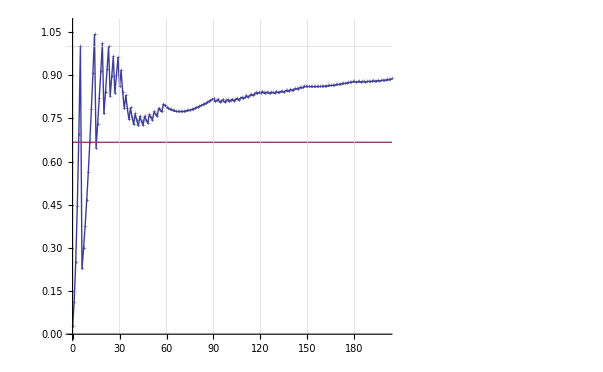

```mathematica
plt=Show[plt2]
```

```mathematica
Export["eff2.eps",plt]
```

eff2.eps

```mathematica
stEff=Table[2/3,{j,0,nmax}];
```

```mathematica
ones=Table[1,{j,0,nmax}];
```

```mathematica
?ListPlot
```

RowBox[{"ListPlot", "[", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["y", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], "]"}] plots points corresponding to a list of values, assumed to correspond to StyleBox["x", "TI"] coordinates 1, 2, …. 
RowBox[{"ListPlot", "[", RowBox[{"{", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["x", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["1", "TR"]]}], "}"}], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["x", "TI"], StyleBox["2", "TR"]], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["2", "TR"]]}], "}"}], ",", StyleBox["…", "TR"]}], "}"}], "]"}] plots a list of points with specified StyleBox["x", "TI"] and StyleBox["y", "TI"] coordinates. 
RowBox[{"ListPlot", "[", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["list", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["list", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], "]"}] plots several lists of points.

```mathematica
0.75^40
```

0.0000100566

```mathematica
36/48 //N
```

0.75

```mathematica
6.5/11 //N
```

0.590909

```mathematica
Ω
```